```mathematica
Quit[]
```

# Demonstrations for the ShkyCovers Package

### Setup

To use the package import it to this notebook.

```mathematica
Import["Schottky.wl"]
```

There are additional two helper packages that the Schottky.wl package uses and are in the setup folder. These are optional to import but have some extra functionalities and function re-definitions that are used in this demonstrations.

```mathematica
Import["setup/Visual.wl"]
Import["setup/Math.wl"]
```

## Defining and Constructing a Schottky Cover

### Full Explicit Construction

#### Defining a Circle

A classical Schottky group is defined is generated by Mobius transformations that map the exterior of a circle to the interior of another circle. We denote a circle by its center and its radius. The setup/Visual.wl package gives a simple way of displaying these circles with the “ComplexCircle” function.

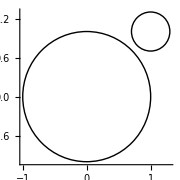

```mathematica
c1 = {0,1};
c2 = {1+I,0.3};
Graphics[{ComplexCircle[c1],ComplexCircle[c2]}
,Axes-> True,ImageSize->Small]
```

#### Obtaining the matrix from a Mobius transformation

A full generator of a Schottky group consists of a pair of circles and the PSL_2(ℂ) matrix corresponding to the Mobius transformation. 
Given a Mobius transformation on can also obtain the corresponding matrix using the “MobiusTransformationToMatrix” function.

```mathematica
γ[z_]:=(2z-3)/(z+I);
```

```mathematica
MobiusTransformationToMatrix[γ]
```

{{(6+4 ⅈ)/(√(-9+46 ⅈ)),-(9+6 ⅈ)/(√(-9+46 ⅈ))},{(3+2 ⅈ)/(√(-9+46 ⅈ)),-(2-3 ⅈ)/(√(-9+46 ⅈ))}}

#### Generating a Mobius transformation from a circle pair

Given a pair of circles one can also generate a Mobius transformation that has the correct properties with “GenerationGetSimpleGeneratorMatrix”.
The map can be obtained with “GenerationGetSimpleGeneratorMap”.

```mathematica
GenerationGetSimpleGeneratorMatrix[c1,c2]//MatrixForm
```

(1+ⅈ | 0.3
1 | 0)

```mathematica
GenerationGetSimpleGeneratorMap[c1,c2][z]
```

(0.3+(1+ⅈ) z)/z

An additional third parameter determines the angle of rotation when mapping one circle to the other.

```mathematica
GenerationGetSimpleGeneratorMatrix[{0,1},{0,0.5}]
```

{{0.5,0.},{0,1}}

```mathematica
GenerationGetSimpleGeneratorMatrix[{0,1},{0,0.5},0.4]
```

{{-0.404508+0.293893 ⅈ,0.+0. ⅈ},{0,1}}

Hence for the following example the point p0=1 will be mapped to the red point when no angle is specified and to the blue when an angle of 0.4 is chosen.
The angle is always defined within the range [0,1).

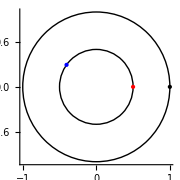

```mathematica
c1={0,1}; c2 = {0,0.5};
γ1 = GenerationGetSimpleGeneratorMap[c1,c2];
γ2 = GenerationGetSimpleGeneratorMap[c1,c2,0.4];
p0=1;
Graphics[{ComplexCircle[c1],ComplexCircle[c2],
ComplexPoint[p0],
Style[ComplexPoint[γ1[p0]],Red],
Style[ComplexPoint[γ2[p0]],Blue]
}
,Axes-> True, ImageSize->Small]
```

## Examples

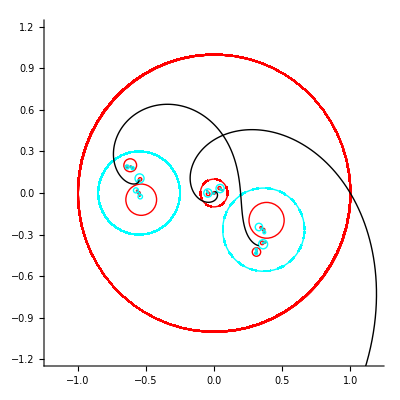

```mathematica
Module[{
c11={0,1},
c12={0,0.1},
c21={-0.55,0.3},
c22={0.45e[0.9],0.3},
c1,c2,C,Γ
},
c1={c11,c12,0.6};
c2={c21,c22,0.7};
C={c1,c2};

Γ=GenerationGetSimpleSchottkyGroup[C];

Graphics[{GraphicsDisplayCover[Γ,5],BranchCutDisplayNormalizedBCycleCurveList[Γ,500,"range"-> {-2,2}]},PlotRange-> GraphicsGetGraphicsRange[Γ],Axes-> True]
]
```

```mathematica
Manipulate[
Module[{
c11={0.7e[1/8],0.4},
c12={0,0.1},
c21={-0.55,0.3},
c22={0.45e[0.9],0.3},
p = x+I y,
c1,c2,C,Γ
},
c1={c11,c12,0.6};
c2={c21,c22,0.7};
C={c1,c2};

Γ=GenerationGetSimpleSchottkyGroup[C];

Graphics[{
GraphicsDisplayCover[Γ,3],
Style[ComplexPoint[#[p]],PointSize[Small]]&/@GroupGetAllMaps[Γ,3],
Style[ComplexPoint[p],Red]
}
,PlotRange-> GraphicsGetGraphicsRange[Γ],Axes-> True]
],
{{x,0.3},-1,1},{{y,0.4},-1,1}
]
```